## Distribución Binomial

## Función de probabilidad y función característica

```mathematica
PDF[BinomialDistribution[n, p], x]
```

Piecewise[{{(1-p)^(n-x) p^x Binomial[n,x], 0≤x≤n}, {0, True}}]

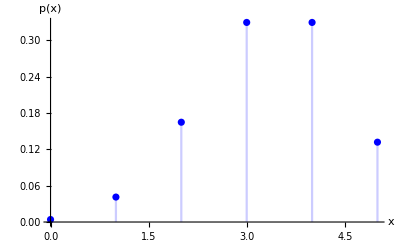

```mathematica
DiscretePlot[PDF[BinomialDistribution[5, 2/3], x], {x, 0, 5.}, PlotStyle->Blue, AxesLabel->{x, p[x]}]
```

```mathematica
CharacteristicFunction[BinomialDistribution[n, p], t] (* directamente *)
```

(1-p+ⅇ^(ⅈ t) p)^n

Mediante la Transformada de Fourier.
Transformada de Fourier en el caso discreto => FourierSequenceTransform, con FourierParameters->{1, -1}.

```mathematica
FourierSequenceTransform[PDF[BinomialDistribution[n, p], x], x, t, FourierParameters->{1, -1}]
```

Piecewise[{{(1+(-1+ⅇ^(ⅈ t)) p)^n, n≥0}, {0, True}}]

Mediante la Esperanza

```mathematica
Expectation[ⅇ^(ⅈ*t*XB), XB\[Distributed]BinomialDistribution[n, p]] (*Esperanza*)
```

(1+(-1+ⅇ^(ⅈ t)) p)^n

Mediante la integral de Lebesgue (sumatorio)

```mathematica
Sum[ⅇ^(ⅈ*t*x)PDF[BinomialDistribution[n, p], x], {x, 0, n}]
```

Piecewise[{{(1-p)^n, n==0}, {(1+(-1+ⅇ^(ⅈ t)) p)^n, True}}]

```mathematica
Simplify[%]
```

(1+(-1+ⅇ^(ⅈ t)) p)^n

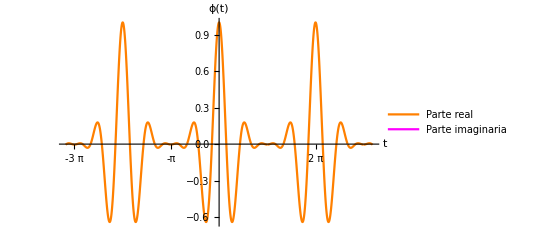

```mathematica
Plot[{Re[CharacteristicFunction[BinomialDistribution[5, 2/3], t]], Im[CharacteristicFunction[BinomialDistribution[, 2/3], t]]}, {t, -10, 10}, PlotStyle->{Orange, Magenta}, AxesLabel->{t, ϕ[t]}, PlotRange->Full, PlotLegends->{"Parte real", "Parte imaginaria"}, Ticks->{{-Pi, -2Pi, -3Pi, Pi, 2Pi, 3Pi}, Automatic}]
```

Verifiquemos la desigualdad de truncamiento

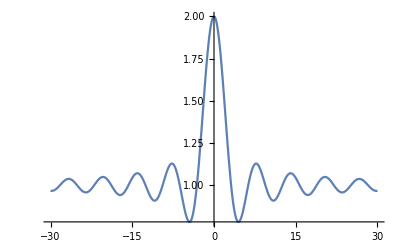

```mathematica
Plot[1+Sin[t]/t, {t, -30, 30}, PlotRange->Full]
```

```mathematica
Limit[1+Sin[t]/t, t->∞]
```

1

```mathematica
k=1/(1+Sin[-1]/1)//N (*k se obtiene con el ínfimo (en t=1)*)
```

6.30799

Cota superior para la probabilidad del complementario de [-a, a]

```mathematica
c[a_]:=k*a*NIntegrate[1-Re[CharacteristicFunction[BinomialDistribution[5, 2/3], t]], {t, 0, 1/a}]
```

Probabilidad para el caso binomial B(5, 2/3)

```mathematica
p[a_]:=1-Probability[-a<=X<=a, X\[Distributed]BinomialDistribution[5, 2/3]]//N
```

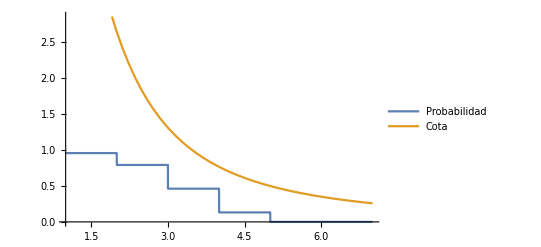

```mathematica
Plot[{p[a], c[a]}, {a, 1, 7}, PlotLegends->{"Probabilidad", "Cota"}]
```

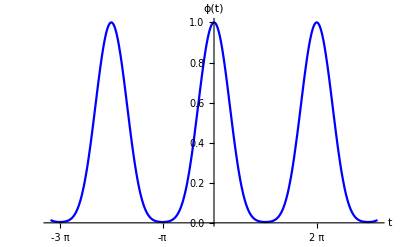

```mathematica
Plot[Abs[CharacteristicFunction[BinomialDistribution[5, 2/3], t]], {t, -10, 10}, PlotStyle->Blue, AxesLabel->{t, ϕ[t]}, PlotRange->Full, Ticks->{{-Pi, -2Pi, -3Pi, Pi, 2Pi, 3Pi}, Automatic}]
```

```mathematica
ParametricPlot3D[{t, Re[CharacteristicFunction[BinomialDistribution[10, 2/3], t]], Im[CharacteristicFunction[BinomialDistribution[10, 2/3], t]]}, {t, -20, 20}, BoxRatios->{1.5, 1, 1}, PlotRange->{{-20, 20}, {-1, 1}, {-1, 1}}, PlotStyle->Red, AxesLabel->{t, Re[ϕ[t]], Im[ϕ[t]]}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{t, Re[CharacteristicFunction[BinomialDistribution[10, 2/3], t]], Im[CharacteristicFunction[BinomialDistribution[10, 2/3], t]]}, {t, -2, 2}, BoxRatios->{1.5, 1, 1}, PlotRange->{{-3, 3}, {-1, 1}, {-1, 1}}, PlotStyle->Blue, AxesLabel->{t, Re[ϕ[t]], Im[ϕ[t]]}, ViewPoint->Right]
```

-Graphics3D-

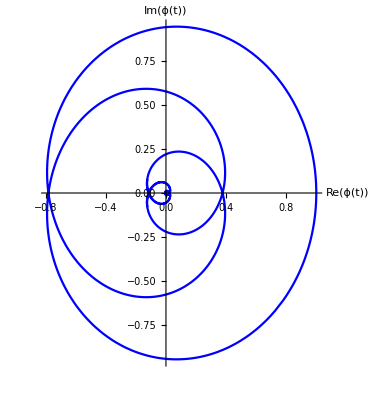

```mathematica
ParametricPlot[{Re[CharacteristicFunction[BinomialDistribution[10, 2/3], t]], Im[CharacteristicFunction[BinomialDistribution[10, 2/3], t]]}, {t, -5, 5}, PlotRange-> All, PlotStyle->Blue, AxesLabel->{Re[ϕ[t]], Im[ϕ[t]]}]
```

## Teorema de inversión

Mediante la Transformada inversa de Fourier

```mathematica
InverseFourierSequenceTransform[(1-p+p*ⅇ^(ⅈ*v))^3, t, x, FourierParameters->{1, -1}]
```

0

Mediante los coeficientes de la serie de Fourier

```mathematica
FourierCoefficient[(1-p+p*ⅇ^(ⅈ*v))^3, t, x]
```

(1-p+ⅇ^(ⅈ v) p)^3 DiscreteDelta[x]

Otras transformaciones:
- Función generatriz de probabilidad (de momentos factoriales)

```mathematica
FactorialMomentGeneratingFunction[BinomialDistribution[n, p], t]
```

(1+p (-1+t))^n

- Función generatriz

```mathematica
GeneratingFunction[PDF[BinomialDistribution[n, p], x], x, t]
```

Piecewise[{{(1+p (-1+t))^n, n≥0}, {0, True}}]

Probabilidades a partir de las derivadas de la función generatiz de probaiblidad

```mathematica
Table[D[FactorialMomentGeneratingFunction[BinomialDistribution[5, p], t], {t, x}]/Factorial[x]/. t-> 0, {x, 0, 5}]
```

{(1-p)^5,5 (1-p)^4 p,10 (1-p)^3 p^2,10 (1-p)^2 p^3,5 (1-p) p^4,p^5}

## Distribución de Cauchy (0, 1)

```mathematica
PDF[CauchyDistribution[], x]
```

1/(π (1+x^2))

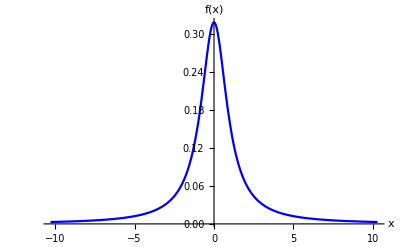

```mathematica
Plot[PDF[CauchyDistribution[], y], {y, -10.3, 10.3}, PlotRange->All, AxesLabel->{x, f[x]}, PlotStyle->Blue]
```

```mathematica
CharacteristicFunction[CauchyDistribution[], t]
```

ⅇ^(-t Sign[t])

Mediante la transformada de Fourier

```mathematica
FourierTransform[PDF[CauchyDistribution[], x], x, t, FourierParameters->{1, 1}]
```

ⅇ^(-Abs[t])

Mediante la integral de Lebesgue (integral)

```mathematica
Integrate[ⅇ^(ⅈ*t*x)*PDF[CauchyDistribution[], x], {x, -∞, ∞}]
```

ConditionalExpression[ⅇ^(-Abs[t]), t∈ℝ]

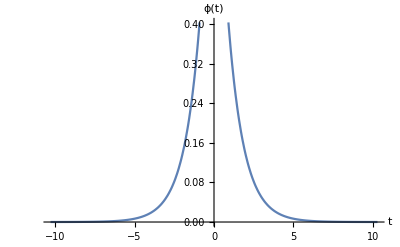

```mathematica
Plot[CharacteristicFunction[CauchyDistribution[], y], {y, -10.3, 10.3}, PlotStyle->All, AxesLabel->{t, ϕ[t]}, PlotStyle->Blue]
```

## Teorema de inversión

Mediante la transformada de Fourier

```mathematica
InverseFourierTransform[ⅇ^(-Abs[t]), FourierParameters->{1, 1}, t, x]
```

1/(π (1+x^2))

## No tiene función generatriz de momentos, pues no tiene momentos

```mathematica
MomentGeneratingFunction[CauchyDistribution[], t]
```

Indeterminate

```mathematica
Moment[CauchyDistribution[], n]
```

Piecewise[{{1, n==0}, {Indeterminate, True}}]

## Teorema de continuidad de Lévy (Teorema central del límite de Moivre)

## Ej: Binomial estandarizadas a Normal (0, 1); (Xn - np)/√npq ⟶ N(0, 1), donde Xn\[Distributed]B(n, p)

Mediante propiedades de la función característica

```mathematica
ⅇ^((-n*p*ⅈ)/Sqrt[n*p*(1-p)])*CharacteristicFunction[BinomialDistribution[n, p], t/Sqrt[n*p*(1-p)]]
```

ⅇ^(-(ⅈ n p)/(√(n (1-p) p))) (1-p+ⅇ^((ⅈ t)/(√(n (1-p) p))) p)^n

Construyendo el modelo

```mathematica
Binomialestandar[n_, p_]:= TransformedDistribution[(Xn-n*p)/Sqrt[n*p*(1-p)], Xn\[Distributed]BinomialDistribution[n, p]]
```

Función característica del modelo

```mathematica
CharacteristicFunction[Binomialestandar[n, p], t]
```

ⅇ^(-(ⅈ n p t)/(√(n (1-p) p))) (1-p+ⅇ^((ⅈ t)/(√(n (1-p) p))) p)^n

Para p = 1/2, el soporte de la distribución es -√n≤ x ≤√n, con diferencia de 2/√n

```mathematica
CharacteristicFunction[Binomialestandar[n, 1/2], t] (* p=1/2 *)
```

ⅇ^(-ⅈ √n t) (1/2+1/2 ⅇ^((2 ⅈ t)/(√n)))^n

```mathematica
pdfBinomialestandar[n_, p_, x_]:=PDF[BinomialDistribution[n, p], Chop[x*Sqrt[n*p*(1-p)]+n*p, 0.1]]
```

```mathematica
pdfBinomialestandar[20, 1/3, 17/Sqrt[20]]
```

0

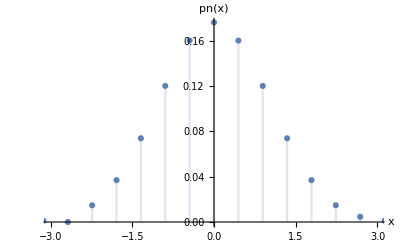

```mathematica
DiscretePlot[pdfBinomialestandar[20,1./2,x],{x,-Sqrt[20],Sqrt[20],2/Sqrt[20]},PlotRange->{{-3,3},All},AxesOrigin->{0,0},AxesLabel->{x,pn[x]}]
```

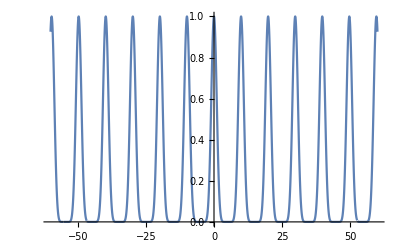

```mathematica
Plot[CharacteristicFunction[Binomialestandar[10, 1./2], t], {t, -60, 60}, PlotRange->All]
```

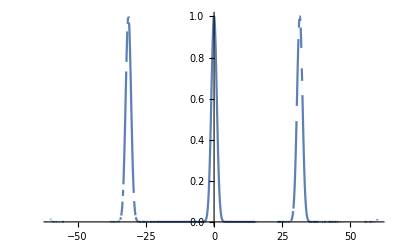

```mathematica
Plot[CharacteristicFunction[Binomialestandar[100, 1./2], t], {t, -60, 60}, PlotRange->All]
```

General::munfl: (0.102863+0.30378 ⅈ)^1000 is too small to represent as a normalized machine number; precision may be lost.

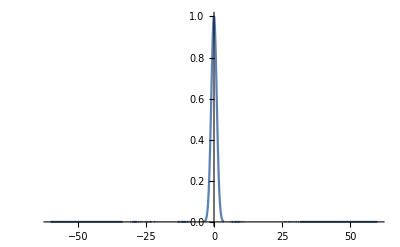

```mathematica
Plot[CharacteristicFunction[Binomialestandar[1000, 1./2], t], {t, -60, 60}, PlotRange->All]
```

Límite de ϕn

```mathematica
DiscreteLimit[CharacteristicFunction[Binomialestandar[n, 1/2], t], n->∞]
```

ⅇ^(-t^2/2)

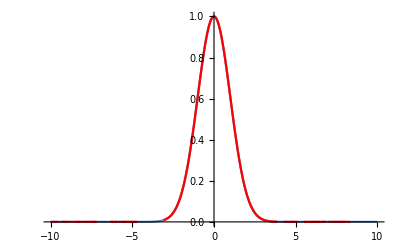

```mathematica
Show[Plot[CharacteristicFunction[NormalDistribution[], t], {t, -10, 10}, PlotRange->All], Plot[CharacteristicFunction[Binomialestandar[1000, 1/2], t], {t, -10, 10}, PlotStyle->Red, PlotRange->All]]
```

Gráfica de la función característica para p = 1/3
Para p = 1/3, el soporte es -√(n/2)≤ x≤ √(2n), con diferencia de 3/(√(2n))

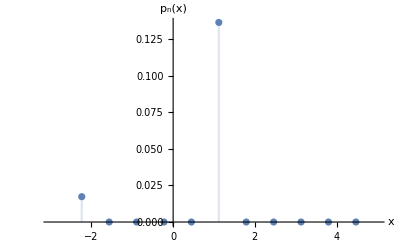

```mathematica
DiscretePlot[pdfBinomialestandar[10,1/3,x],{x,-√5,√20,3/√20},
PlotRange->{{-3,5},All},AxesOrigin->{0,0},AxesLabel->{x,Subscript[p, n][x]}]
```

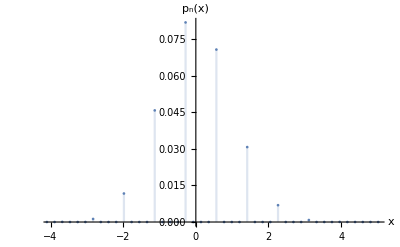

```mathematica
DiscretePlot[pdfBinomialestandar[100,1/3,x],{x,-√50,√200,3/√200},
PlotRange->{{-4,5},All},AxesOrigin->{0,0},AxesLabel->{x,Subscript[p, n][x]}]
```

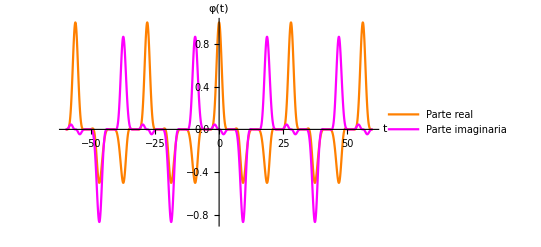

```mathematica
Plot[{Re[CharacteristicFunction[Binomialestandar[10,1/3],t]],Im[CharacteristicFunction[Binomialestandar[10,1/3],t]]},{t,-60,60},PlotStyle->{Orange,Magenta},AxesLabel->{t,φ[t]},PlotRange->Full,PlotLegends->{"Parte real","Parte imaginaria"}]
```

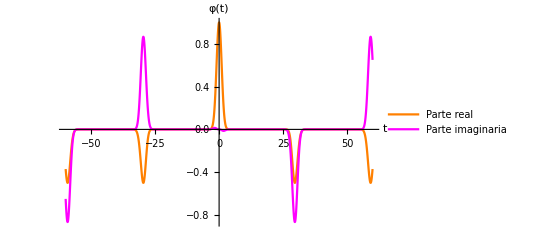

```mathematica
Plot[{Re[CharacteristicFunction[Binomialestandar[100,1/3],t]],Im[CharacteristicFunction[Binomialestandar[100,1/3],t]]},{t,-60,60},PlotStyle->{Orange,Magenta},AxesLabel->{t,φ[t]},PlotRange->Full,PlotLegends->{"Parte real","Parte imaginaria"}]
```

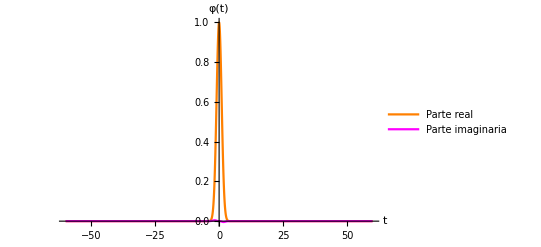

```mathematica
Plot[{Re[CharacteristicFunction[Binomialestandar[1000,1/3],t]],Im[CharacteristicFunction[Binomialestandar[1000,1/3],t]]},{t,-60,60},PlotStyle->{Orange,Magenta},AxesLabel->{t,φ[t]},PlotRange->Full,PlotLegends->{"Parte real","Parte imaginaria"}]
```

```mathematica
DiscreteLimit[CharacteristicFunction[Binomialestandar[n,1/3],t],n->∞]
```

ⅇ^(-t^2/2)

```mathematica
DiscreteLimit[CharacteristicFunction[Binomialestandar[n,p],t],n->∞]
```

ⅇ^(-t^2/2)